# Superconducting qubits Hub

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

## Configuration of the virtual superconducting device

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
QubitNum -> 6,
(* The T1 time *)
T1 -> <|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2 -> <|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit -> <|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq -> <|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for the edge notation *)
ExchangeCoupling -> <|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity -> <|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead -> <|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas -> 5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy -> 0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX -> 0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ -> 0.5,
(* switches to turn on/off standard passive noise, i.e., T1 and T2 decay *)
StdPassiveNoise -> True,
(* switches to turn on/off the cross-talk ZZ-noise *)
ZZPassiveNoise -> True
};
```

## Elementary guide

### Native gates

(* initialisation and readout *)
Init_q, M_q
(* single-qubit gates *)
Rx_q[θ], Ry_q[θ], Rz_q[θ], where  θ ϵ [-π, π] 
(* two-qubit gates: siZZler and cross-resonant *)
ZZ_(q1,q2) , ZX_(q1, q2)
(* others: wait or doing nothing *)
Wait_q[Δt]

### Instantiate the VQD and show connectivity

```mathematica
dev=SuperconductingHub[];
```

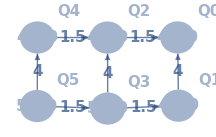

```mathematica
g=dev[Connectivity]
```

### Passive noise test

```mathematica
noisycirc = 
InsertCircuitNoise[
{Sequence @@ (Subscript[Init, #]& /@ Range[0,5]),Subscript[Rx, 0][π],Subscript[Rx, 1][π],Subscript[Rx, 3][π/2],Subscript[ZX, 1,0],Subscript[ZZ, 4,5],Subscript[Rx, 0][π/4],Subscript[Rx, 1][π],Subscript[Rx, 2][π],Subscript[ZX, 2,0],Subscript[M, 0]},
SuperconductingHub[],ReplaceAliases->True];
```

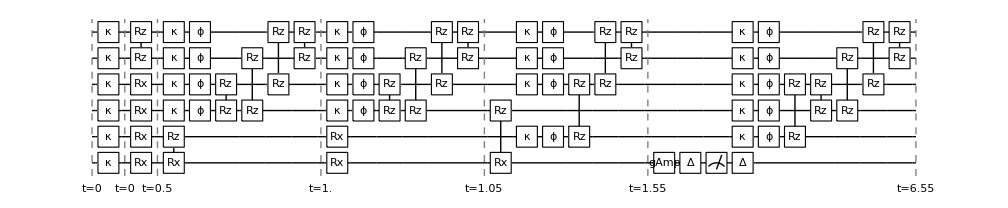

```mathematica
DrawCircuit[noisycirc]
```

### State initialisation to the thermal state

```mathematica
DestroyAllQuregs[];
ρinit=CreateDensityQureg[6];
ρ=CreateDensityQureg[6];
```

The population prepared state should be in the mixture  ρ_thermal = p|0X0|+(1-p)|1X1|, where p is specified in ExcitedInit.
This is done by applying Init operator to each qubit which is done only in the very beginning.

```mathematica
Values@OptionValue[SuperconductingHub,ExcitedInit]
```

{0.032,0.021,0.008,0.009,0.025,0.007}

```mathematica
(* the init operator in terms of noise *)
noisycirc=InsertCircuitNoise[Subscript[Init, #]& /@ Range[0,5],SuperconductingHub[],ReplaceAliases->True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.}},{{0.,0.98387},{0.,0.}},{{0.,0.},{0.,0.178885}},{{0.,0.},{0.178885,0.}}}],Kraus_1[{{{0.989444,0.},{0.,0.}},{{0.,0.989444},{0.,0.}},{{0.,0.},{0.,0.144914}},{{0.,0.},{0.144914,0.}}}],Kraus_2[{{{0.995992,0.},{0.,0.}},{{0.,0.995992},{0.,0.}},{{0.,0.},{0.,0.0894427}},{{0.,0.},{0.0894427,0.}}}],Kraus_3[{{{0.99549,0.},{0.,0.}},{{0.,0.99549},{0.,0.}},{{0.,0.},{0.,0.0948683}},{{0.,0.},{0.0948683,0.}}}],Kraus_4[{{{0.987421,0.},{0.,0.}},{{0.,0.987421},{0.,0.}},{{0.,0.},{0.,0.158114}},{{0.,0.},{0.158114,0.}}}],Kraus_5[{{{0.996494,0.},{0.,0.}},{{0.,0.996494},{0.,0.}},{{0.,0.},{0.,0.083666}},{{0.,0.},{0.083666,0.}}}]},{}},{0,{},{}}}

```mathematica
(* initialise matrix as a random mix state of 6 qubits, then apply the initialisation command *)
SetQuregMatrix[ρinit,RandomMixState[6]];
```

```mathematica
(* apply the noisy circuit, then check the diagonal of the density matrix *)
ApplyCircuit[ρinit,ExtractCircuit @ noisycirc];
Diagonal @ Chop@ Re @ GetQuregMatrix[ρinit]
```

{0.901981,0.0298175,0.0193479,0.0006396,0.00727404,0.000240464,0.000156031,5.15806×10^-6,0.00819155,0.000270795,0.000175713,5.80868×10^-6,0.0000660609,2.18383×10^-6,1.41704×10^-6,4.68442×10^-8,0.0231277,0.000764552,0.0004961,0.0000164,0.000186514,6.16575×10^-6,4.00081×10^-6,1.32258×10^-7,0.00021004,6.94346×10^-6,4.50545×10^-6,1.4894×10^-7,1.69387×10^-6,5.59957×10^-8,3.63343×10^-8,1.20113×10^-9,0.00635837,0.000210194,0.00013639,4.50876×10^-6,0.0000512772,1.69511×10^-6,1.09992×10^-6,3.6361×10^-8,0.0000577451,1.90893×10^-6,1.23866×10^-6,4.09474×10^-8,4.65686×10^-7,1.53946×10^-8,9.98918×10^-9,3.30221×10^-10,0.000163035,5.38959×10^-6,3.49718×10^-6,1.15609×10^-7,1.3148×10^-6,4.34645×10^-8,2.82031×10^-8,9.32333×10^-10,1.48064×10^-6,4.89469×10^-8,3.17605×10^-8,1.04993×10^-9,1.19407×10^-8,3.94733×10^-10,2.56133×10^-10,0}

```mathematica
(* Sanity check: the diagonals should be as follows *)
Reverse @ Chop @ Diagonal[KroneckerProduct@@({{#,0},{0,1-#}}&/@(Reverse @ Values @ OptionValue[SuperconductingHub,ExcitedInit]))]
```

{0.901981,0.0298175,0.0193479,0.0006396,0.00727404,0.000240464,0.000156031,5.15806×10^-6,0.00819155,0.000270795,0.000175713,5.80868×10^-6,0.0000660609,2.18383×10^-6,1.41704×10^-6,4.68442×10^-8,0.0231277,0.000764552,0.0004961,0.0000164,0.000186514,6.16575×10^-6,4.00081×10^-6,1.32258×10^-7,0.00021004,6.94346×10^-6,4.50545×10^-6,1.4894×10^-7,1.69387×10^-6,5.59957×10^-8,3.63343×10^-8,1.20113×10^-9,0.00635837,0.000210194,0.00013639,4.50876×10^-6,0.0000512772,1.69511×10^-6,1.09992×10^-6,3.6361×10^-8,0.0000577451,1.90893×10^-6,1.23866×10^-6,4.09474×10^-8,4.65686×10^-7,1.53946×10^-8,9.98918×10^-9,3.30221×10^-10,0.000163035,5.38959×10^-6,3.49718×10^-6,1.15609×10^-7,1.3148×10^-6,4.34645×10^-8,2.82031×10^-8,9.32333×10^-10,1.48064×10^-6,4.89469×10^-8,3.17605×10^-8,1.04993×10^-9,1.19407×10^-8,3.94733×10^-10,2.56133×10^-10,0}

### Thermal state (ρinit) can be prepared by waiting

```mathematica
noisycirc=InsertCircuitNoise[{ Subscript[Wait, #][1]& /@ Range[0,5]},SuperconductingHub[],ReplaceAliases -> True]
```

{{0,{Kraus_0[{{{0.98387,0.},{0.,0.976092}},{{0.,0.123466},{0.,0.}},{{0.177471,0.},{0.,0.178885}},{{0.,0.},{0.0224483,0.}}}],Deph_0[0.00440526],Kraus_1[{{{0.989444,0.},{0.,0.984139}},{{0.,0.102325},{0.,0.}},{{0.144137,0.},{0.,0.144914}},{{0.,0.},{0.0149866,0.}}}],Deph_1[0.00334447],R[0.131923,Z_0 Z_1],Kraus_2[{{{0.995992,0.},{0.,0.991434}},{{0.,0.0951803},{0.,0.}},{{0.0890334,0.},{0.,0.0894427}},{{0.,0.},{0.00854745,0.}}}],Deph_2[0.00269541],R[-0.0277977,Z_0 Z_2],Kraus_3[{{{0.99549,0.},{0.,0.991171}},{{0.,0.0926285},{0.,0.}},{{0.0944568,0.},{0.,0.0948683}},{{0.,0.},{0.00882732,0.}}}],Deph_3[0.00309597],R[-0.0273321,Z_1 Z_3],R[0.133003,Z_2 Z_3],Kraus_4[{{{0.987421,0.},{0.,0.980187}},{{0.,0.119303},{0.,0.}},{{0.156956,0.},{0.,0.158114}},{{0.,0.},{0.0191038,0.}}}],Deph_4[0.00408161],R[-0.0276241,Z_2 Z_4],Kraus_5[{{{0.996494,0.},{0.,0.992516}},{{0.,0.0889512},{0.,0.}},{{0.083332,0.},{0.,0.083666}},{{0.,0.},{0.00746837,0.}}}],Deph_5[0.00249376],R[-0.0274045,Z_3 Z_5],R[0.132693,Z_4 Z_5]},{}},{1,{},{}}}

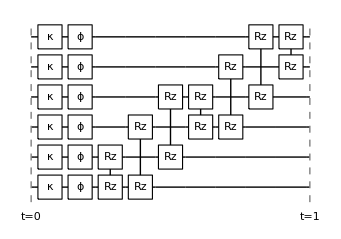

```mathematica
DrawCircuit[noisycirc]
```

```mathematica
(* wait for t, then check fidelity to the thermal state ρinit *)
δt=4;
SetQuregMatrix[ρ,RandomMixState[6]];
data=Table[
ApplyCircuit[ρ,ExtractCircuit @ InsertCircuitNoise[Subscript[Wait, #][δt]& /@ Range[0,5],SuperconductingHub[],ReplaceAliases->True]];
{t,CalcFidelityDensityMatrices[ρ, ρinit]}
,{t, δt, 440, δt}];
```

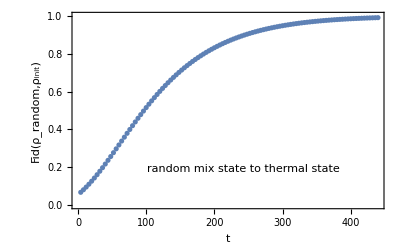

```mathematica
ListPlot[data,
PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ_random,ρ_init)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["random mix state to thermal state",Scaled[{0.55,0.2}]]
]
```

### Free induction decay: T1 experiment

```mathematica
δt = 4;
SetQuregMatrix[ρ,RandomMixState[6]];
dataT1 = Table[
dev=SuperconductingHub[];
ApplyCircuit[ρ,ExtractCircuit @ InsertCircuitNoise[Subscript[Init, #]& /@ Range[0,5],dev,ReplaceAliases -> True]];
ApplyCircuit[ρ,ExtractCircuit @ InsertCircuitNoise[Subscript[Rx, #][π]& /@ Range[0,5],dev,ReplaceAliases -> True]];
ApplyCircuit[ρ,ExtractCircuit @ InsertCircuitNoise[Subscript[Wait, #][t]& /@ Range[0,5],dev,ReplaceAliases -> True]];
{t, CalcProbOfOutcome[ρ,#,1]}& /@ Range[0,5]
,{t, 0, 500, δt}];
```

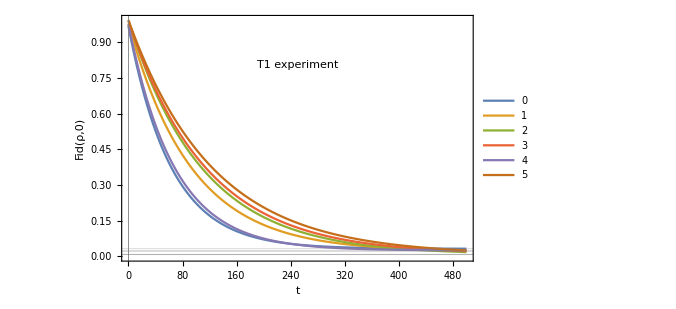

```mathematica
(* expected probability at T -> ∞, denoted by grey lines *)
expectedprob=Values@OptionValue[SuperconductingHub,ExcitedInit];
ListPlot[Transpose[dataT1],
Frame -> True, PlotLegends -> Placed[Range[0,5],{0.9,0.5}], GridLines -> {expectedprob}, Frame -> True, FrameLabel -> {"t", "Fid(ρ,0)"},FrameStyle -> Directive[Black,Thick], ImageSize -> 500, BaseStyle -> {17}, Epilog -> Inset["T1 experiment", Scaled[{0.5, 0.8}]], Joined -> True
]
```

### Free induction decay: T2 experiment

```mathematica
δt = 4;
SetQuregMatrix[ρ, RandomMixState[6]];
dataT2 = Table[
dev = SuperconductingHub[];
ApplyCircuit[ρ, ExtractCircuit @ InsertCircuitNoise[Subscript[Init, #]& /@ Range[0, 5],dev,ReplaceAliases -> True]];
ApplyCircuit[ρ, ExtractCircuit @ InsertCircuitNoise[Flatten[Subscript[Ry, #][π/2]&/@ Range[0, 5]],dev,ReplaceAliases -> True]];
ApplyCircuit[ρ, ExtractCircuit @ InsertCircuitNoise[Subscript[Wait, #][t]&/@ Range[0, 5],dev,ReplaceAliases -> True]];
ApplyCircuit[ρ, ExtractCircuit @ InsertCircuitNoise[Flatten[Subscript[Ry, #][-π/2]& /@ Range[0, 5]],dev,ReplaceAliases -> True]];
{t, CalcProbOfOutcome[ρ,#, 0]}&/@ Range[0, 5]
,{t, 0, 500, δt}];
```

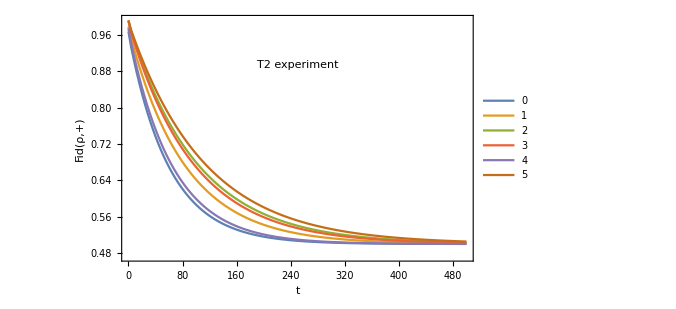

```mathematica
ListPlot[Transpose[dataT2], PlotLegends -> Placed[Range[0, 5],{0.9, 0.55}], PlotRange -> All, Frame -> True, FrameStyle -> Directive[Black, Thick],ImageSize->500, FrameLabel -> {"t","Fid(ρ,+)"}, BaseStyle->{17}, Epilog -> Inset["T2 experiment", Scaled[{0.5, 0.8}]], Joined -> True]
```

## Paper supplement: VQE of H_2 on the superconducting qubit

Modules

```mathematica
(* The virtual device works only for θ ϵ [-π, π] ]*)
angleToMinusPiToPi[angle_]:=Mod[angle+π,2 π]-π
```

Load the data

```mathematica
(* exact ground state energies *)
gsH2<<"supplement/VQEonSuperconductingHub/gsH2.mx";
(* noiseless *)
vqeH20<<"supplement/VQEonSuperconductingHub/run1/vqeH20.mx";
 (*realistic noise *)
vqeH21<<"supplement/VQEonSuperconductingHub/run1/vqeH21.mx";
(* static noise only *)
vqeH22<<"supplement/VQEonSuperconductingHub/run1/vqeH22.mx";
```

```mathematica
data=Join[
{Values@gsH2[[All, {"distance", "groundstate"}]]},
 Values @ #[[All, {"distance", "cost"}]]& /@ {vqeH20, vqeH21, vqeH22}
];
```

```mathematica
colors={RGBColor[0.762728865113008, 0.14145836106631227, 0.39636199524817384],RGBColor[0.35196374646090467, 0.5413118001875443, 0.4414109963939472],RGBColor[0.08381075950145633, 0.3311271299900129, 0.5731766325728749],RGBColor[0.7572732231089121, 0.3397554900882702, 0.07649872068397667]};
```

```mathematica
(* molecule image *)
H2=ImageResize[MoleculePlot3D[Molecule[ConstantArray["H", 2], Bond[{#, #+1}, "Single"]& /@ Range[1], AtomCoordinates -> ({.8*#, 0, 0}& /@ Range[0, 1])]], 140]
```

-Graphics-

```mathematica
Show[
ListPlot[Values/@gsH2[[All,{"distance","groundstate"}]],Joined->True,PlotStyle->Directive[colors[[1]],Thickness->Scaled[0.006]],BaseStyle->{11,FontFamily->"Serif"},Epilog->Inset[H2,Scaled[{0.8,0.92}]]],
ListPlot[Values@#[[All,{"distance","cost"}]]&/@{vqeH20,vqeH21,vqeH22},PlotMarkers->{Automatic,5},PlotStyle->{Directive[colors[[2]]
,Dashed,Thickness->Scaled[0.002]],Directive[colors[[3]],Dashed],Directive[colors[[4]],Dotted]},Joined->True],
Frame->True,FrameStyle->Directive[Black,Thick],Background->White
,Epilog->Inset[Column[{H2,LineLegend[colors,{"Exact","Noiseless","Realistic noise","Static noise only"},Spacings->0.,LegendFunction->Framed,LegendMargins->0]},Alignment->Center],Scaled[{0.75,0.28}]],BaseStyle->{12,FontFamily->"Serif"},FrameLabel->{"atomic distance (Angstrom)","Energy (Ha)"},ImageSize->400,AspectRatio->0.7,ImagePadding->{{60, 5}, {45, 5}}
]
(*Export["/home/cica/vqd/img/vqeh2.pdf",%]*)
```

-Graphics-

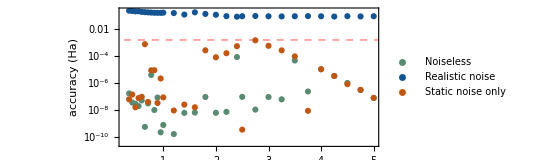

```mathematica
yticks={{10^-10, "10^-10"}, {10^-8, "10^-8"}, {10^-6, "10^-6"}, {10^-6, "10^-6"}, {10^-4, "10^-4"}, {0.0015, "chem"}, {0.1, "0.1"}};
ListLogPlot[
{
Transpose @ {vqeH20[[All, "distance"]], vqeH20[[All, "cost"]] - vqeH20[[All, "groundstate"]]},
Transpose @ {vqeH21[[All, "distance"]], vqeH21[[All, "cost"]] - vqeH21[[All, "groundstate"]]},
Transpose @ {vqeH22[[All, "distance"]], vqeH22[[All, "cost"]] - vqeH21[[All, "groundstate"]]}},
Frame -> True, FrameStyle -> Directive[Black, Thick], Background -> White, PlotRange -> All,
GridLines -> {None,  {0.0015}}, GridLinesStyle -> Directive[Thick, Dashed, Red],FrameTicks -> {{yticks, Automatic}, {Automatic, Automatic}},
FrameLabel -> {None, "accuracy (Ha)"}, PlotLegends -> PointLegend[Automatic, {"Noiseless", "Realistic noise", "Static noise only"}, LegendMargins -> 0, LegendMarkerSize -> 15],
ImageSize -> 400, AspectRatio -> 0.4, LabelStyle -> {11, FontFamily -> "Serif"}, ImagePadding -> {{60,  5}, {15, 5}},PlotStyle -> colors[[2;;]]
]
(*Export["/home/cica/vqd/img/vqeh2err.pdf",%]*)
```